## Pivoting Code

### Helper Coder argMax etc.

Making a helper code that gives the location of the largest entry (in absolute value) on or past the kth entry of a vector.

```mathematica
?Ordering
```

```mathematica
argMax[aIn_,k_]:= Module[{a=Abs[aIn]},
a⟦1;;k-1⟧*=0.0; 
FirstPosition[a,Max[a]][[1]]
]
```

Testing.

```mathematica
{m,k}={8,3};
a=RandomReal[{-1,1},m];
argMax[a,k]
TableForm[Abs[a],TableHeadings->Automatic]
```

8

1 | 0.555815
2 | 0.184018
3 | 0.209094
4 | 0.28003
5 | 0.120989
6 | 0.328386
7 | 0.534939
8 | 0.838109

For complete pivoting we need to find the position {i,j} of the largest entry in the bottom block past the (k,k) entry.  Not sure if it is worth making a function

```mathematica
{m,k}={6,3};
AIn=RandomReal[{-1,1},{m,m}];
A=Abs[AIn];
A⟦All,1;;k-1⟧*=0.0;
A⟦1;;k-1,All⟧*=0.0;
Position[A,Max[A]]⟦1⟧
TableForm[A,TableHeadings->Automatic]
```

{4,6}

| 1 | 2 | 3 | 4 | 5 | 6
1 | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0.0833266 | 0.252946 | 0.593128 | 0.239908
4 | 0. | 0. | 0.0256838 | 0.197357 | 0.881071 | 0.936255
5 | 0. | 0. | 0.12678 | 0.745966 | 0.557494 | 0.304179
6 | 0. | 0. | 0.852567 | 0.146622 | 0.708255 | 0.175508

### Pivot Finding Strategies

Strategies
Row: 		Find largest entry in the last part of the appropriate column.
Column:		Find the largest entry in the last part of the appropriate row.
Complete:	Find the largest entry in the lower block of the matrix.
Rook:		Find an  entry that dominates its row and column.

```mathematica
PivotRow[A_,k_]:=Module[{col=A⟦All,k⟧},
(* Extract column find row to swap *)
argMax[a,k]
]
PivotCol[A_,k_]:=Module[{row=A⟦k,All⟧},
(* Extract row find column to swap *)
argMax[row,k]
]
PivotComplete[A_,k_]:=Module[{block=Abs[A]},
(* Extract block find row and column to swap *)
block⟦All,1;;k-1⟧*=0.0;
block⟦1;;k-1,All⟧*=0.0;
Position[block,Max[block]]⟦1⟧
]
PivotRook[A_,k_]:=Module[{block=Abs[A],i,j,row,col},
(* search rows and columns until you *)
(* find a dominating entry *)
(* start with a column pivot search *)
j=k;
row=block⟦All,j⟧;
i=argMax[row,k];


  
j=Pivot[Col,
block⟦1;;k-1,All⟧*=0.0;
Position[block,Max[block]]⟦1⟧
]
```

```mathematica
ArgMax
```

```mathematica
argMax[a_,k_]:=
```

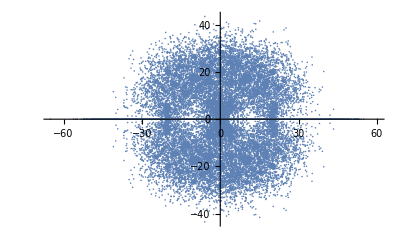

```mathematica
SampleSize=10^4;
m=5;
RectangularData=Table[
A=RandomChoice[{-20.0,-1.0,0.0,1.0,20.0},{m,m}];Eigenvalues[A],
{SampleSize}];
FlatData=Flatten[RectangularData];
ListPlot[ReIm[FlatData]]
```

I can see the picture emerging!

```mathematica
a=Ceiling[Max[Abs[Flatten[FlatData]]]];
d=4096;
Δλ=2a/(d-1);
DataCounts=ConstantArray[1.0,{d,d}];
Dimensions[DataCounts]
```

{4096,4096}

```mathematica
Do[
i=1+Floor[(Re[λ]+a)/Δλ];
j=1+Floor[(Im[λ]+a)/Δλ];
DataCounts⟦i,j⟧+=1,
{λ,FlatData}]
```

```mathematica
ListDensityPlot[Log[DataCounts],PlotLegends->Automatic]
```

-Graphics-

```mathematica
DataCounts⟦1;;12,1;;12⟧
```

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}}

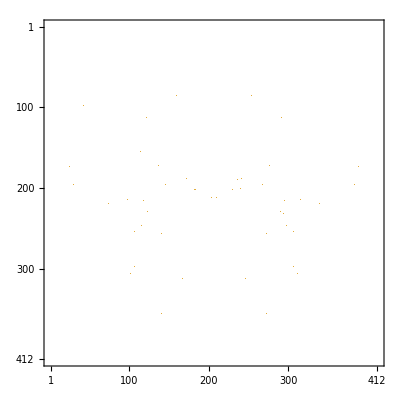

```mathematica
MatrixPlot[DataCounts]
```

```mathematica
ListDensityPlot[DataCounts]
```

-Graphics-

```mathematica
?BinCounts
```

```mathematica
?BinCounts
```

```mathematica
?DensityPlot
```

```mathematica
?Histogram3D
```